0.7 x+0.5 x^2+0.2 Log[x]+2.4485 x Log[x]+1.12834 Log[x]^2+0.3 Log[1+x]

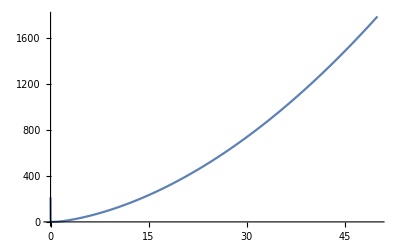

```mathematica
func=a*x+b*x^2+c*Log[x]+d*Log[1+x]+e*(Log[x])^2+f*(x*Log[x]);
subst={a->0.7,b->0.5,c->0.2,d->0.3,e->5*RandomReal[],f->3*RandomReal[]};
testfunc=func/.subst
Plot[testfunc,{x,0,50}]
```

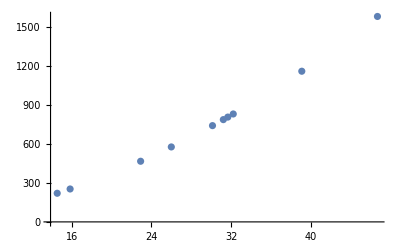

```mathematica
nDatapoint=10000;
noise=0.1*RandomReal[];
randomX=Table[RandomReal[{1,50}],{i,nDatapoint}];
Y=Table[testfunc/.x->randomX[[i]],{i,nDatapoint}];
randomY=Table[Y[[i]]+RandomReal[{-noise,noise}],{i,nDatapoint}];
XY=Thread[{randomX,randomY}];
ListPlot[XY]
```

```mathematica
ClearAll["basisvector"]
ClearAll["curve0"]
ClearAll["w"]
ClearAll["errorfunc"]
```

```mathematica
basisvector[x_]={x,x^2,Log[x],Log[1+x], (Log[x])^2,x*Log[x]};
curve0[x_]=Transpose[w].basisvector[x];
η=10^-11(*Learning rate*);
iternation=4000;
```

```mathematica
weight2=Table[0,6];
weight1= Table[RandomReal[],6](*RandomReal[{1,2}]*)
```

{0.225329,0.847378,0.157259,0.786963,0.642339,0.829046}

```mathematica
curve1[x_]=Transpose[weight1].basisvector[x];
For[i=1,i<iternation,i++, weight2=weight1+η*((randomY[[i]]-curve1[randomX[[i]]])*basisvector[randomX[[i]]])];
weight2
```

Part::partw: Part 11 of {253.475,787.7,831.159,577.265,467.048,807.174,1582.18,741.435,220.512,1160.39} does not exist.

Part::partw: Part 11 of {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{0.225329+1/100000000000{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧ (-0.157259 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.642339 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]^2-0.786963 Log[1+{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.225329 {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.829046 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.847378 ({15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧)^2+{253.475,787.7,831.159,577.265,467.048,807.174,1582.18,741.435,220.512,1160.39}⟦3999⟧),0.847378+1/100000000000({15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧)^2 (-0.157259 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.642339 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]^2-0.786963 Log[1+{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.225329 {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.829046 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.847378 ({15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧)^2+{253.475,787.7,831.159,577.265,467.048,807.174,1582.18,741.435,220.512,1160.39}⟦3999⟧),0.157259+1/100000000000 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] (-0.157259 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.642339 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]^2-0.786963 Log[1+{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.225329 {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.829046 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.847378 ({15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧)^2+{253.475,787.7,831.159,577.265,467.048,807.174,1582.18,741.435,220.512,1160.39}⟦3999⟧),0.786963+1/100000000000 Log[1+{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] (-0.157259 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.642339 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]^2-0.786963 Log[1+{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.225329 {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.829046 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.847378 ({15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧)^2+{253.475,787.7,831.159,577.265,467.048,807.174,1582.18,741.435,220.512,1160.39}⟦3999⟧),0.642339+1/100000000000 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]^2 (-0.157259 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.642339 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]^2-0.786963 Log[1+{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.225329 {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.829046 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.847378 ({15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧)^2+{253.475,787.7,831.159,577.265,467.048,807.174,1582.18,741.435,220.512,1160.39}⟦3999⟧),0.829046+1/100000000000 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧ (-0.157259 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.642339 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]^2-0.786963 Log[1+{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧]-0.225329 {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.829046 Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧-0.847378 ({15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧)^2+{253.475,787.7,831.159,577.265,467.048,807.174,1582.18,741.435,220.512,1160.39}⟦3999⟧)}

```mathematica
curve2[x]=Transpose[weight2].basisvector[x];
curve=curve2[x];
Y2=Table[curve/.x->randomX[[i]],{i,nDatapoint}];
randomY2=Table[Y2[[i]],{i,nDatapoint}];
```

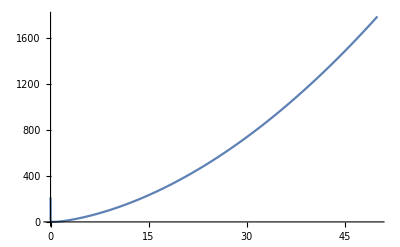

```mathematica
p1=Plot[curve,{x,0,50},PlotStyle->Red];
p2=Plot[testfunc,{x,0,50}];
Show[p1,p2]
```

```mathematica
trainingset=Table[randomX[[j]]->randomY2[[j]],{j,iternation}];
testset=Table[randomX[[nDatapoint-j]]->randomY2[[nDatapoint-j]],{j,(nDatapoint-iternation)}];
```

Part::partw: Part 11 of {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112} does not exist.

Part::partw: Part 11 of {2.76206 (0.157259+(Log[{«10»}⟦3999⟧] (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧))/100000000000)+7.62897 (0.642339+(Log[Part[«2»]]^2 («11»+{«10»}⟦3999⟧))/100000000000)+2.82331 (0.786963+(«1» «1»)/(10«8»00))+«19» «1»+43.73 (0.829046+(Log[{«10»}⟦3999⟧] {«1»}⟦3999⟧ («1»))/100000000000)+250.665 (0.847378+(({«10»}⟦3999⟧)^2 («11»+{«10»}⟦3999⟧))/100000000000),«8»,«1»} does not exist.

Part::partw: Part 12 of {15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
p=Predict[trainingset];
PredictorMeasurements[p,testset,"MeanSquare"]
```

Part::partw: Part 11 of {2.76206 (0.157259+1.×10^-11 Log[{«10»}⟦3999⟧] (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧))+«4»+250.665 (0.847378+1.×10^-11 ({«10»}⟦3999⟧)^2 (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧)),«8»,3.66643 (0.157259+«1»)+«4»+«19» («1»)} does not exist.

Part::partw: Part 12 of {2.76206 (0.157259+1.×10^-11 Log[{«10»}⟦3999⟧] (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧))+«4»+250.665 (0.847378+1.×10^-11 ({«10»}⟦3999⟧)^2 (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧)),«8»,3.66643 (0.157259+«1»)+«4»+«19» («1»)} does not exist.

Part::partw: Part 13 of {2.76206 (0.157259+1.×10^-11 Log[{«10»}⟦3999⟧] (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧))+«4»+250.665 (0.847378+1.×10^-11 ({«10»}⟦3999⟧)^2 (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧)),«8»,3.66643 (0.157259+«1»)+«4»+«19» («1»)} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value (2.76206 (0.157259+(Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] («1»))/100000000000)+7.62897 (0.642339+(Log[{«10»}⟦3999⟧]^2 («1»))/100000000000)+2.82331 (0.786963+(Log[1+«1»] «1»)/100000000000)+«19» («1»)+43.73 (0.829046+(«1»)/100000000000)+250.665 (0.847378+(({15.8324,31.2285,«7»,39.112}⟦3999⟧)^2 («1»))/100000000000)).

PredictorMeasurements::wrgfunc: The first argument should be a predictor, a list of predictions, or a list of distributions instead of Predict[<<1084467504 bytes>>].

Part::partw: Part 11 of {2.76206 (0.157259+(Log[{«10»}⟦3999⟧] (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧))/100000000000)+7.62897 (0.642339+(Log[Part[«2»]]^2 («11»+{«10»}⟦3999⟧))/100000000000)+2.82331 (0.786963+(«1» «1»)/(10«8»00))+«19» «1»+43.73 (0.829046+(Log[{«10»}⟦3999⟧] {«1»}⟦3999⟧ («1»))/100000000000)+250.665 (0.847378+(({«10»}⟦3999⟧)^2 («11»+{«10»}⟦3999⟧))/100000000000),«8»,«1»} does not exist.

Part::partw: Part 12 of {2.76206 (0.157259+(Log[{«10»}⟦3999⟧] (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧))/100000000000)+7.62897 (0.642339+(Log[Part[«2»]]^2 («11»+{«10»}⟦3999⟧))/100000000000)+2.82331 (0.786963+(«1» «1»)/(10«8»00))+«19» «1»+43.73 (0.829046+(Log[{«10»}⟦3999⟧] {«1»}⟦3999⟧ («1»))/100000000000)+250.665 (0.847378+(({«10»}⟦3999⟧)^2 («11»+{«10»}⟦3999⟧))/100000000000),«8»,«1»} does not exist.

Part::partw: Part 13 of {2.76206 (0.157259+(Log[{«10»}⟦3999⟧] (-0.157259 Log[«1»]-0.642339 Power[«2»]-0.786963 Log[«1»]-0.225329 Part[«2»]-0.829046 Log[«1»] Part[«2»]-0.847378 Power[«2»]+{«10»}⟦3999⟧))/100000000000)+7.62897 (0.642339+(Log[Part[«2»]]^2 («11»+{«10»}⟦3999⟧))/100000000000)+2.82331 (0.786963+(«1» «1»)/(10«8»00))+«19» «1»+43.73 (0.829046+(Log[{«10»}⟦3999⟧] {«1»}⟦3999⟧ («1»))/100000000000)+250.665 (0.847378+(({«10»}⟦3999⟧)^2 («11»+{«10»}⟦3999⟧))/100000000000),«8»,«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value (2.76206 (0.157259+(Log[{15.8324,31.2285,32.2251,26.0013,22.9171,31.6783,46.7154,30.1389,14.5356,39.112}⟦3999⟧] («1»))/100000000000)+7.62897 (0.642339+(Log[{«10»}⟦3999⟧]^2 («1»))/100000000000)+2.82331 (0.786963+(Log[1+«1»] «1»)/100000000000)+«19» («1»)+43.73 (0.829046+(«1»)/100000000000)+250.665 (0.847378+(({15.8324,31.2285,«7»,39.112}⟦3999⟧)^2 («1»))/100000000000)).

$Aborted[]